# Garoa Hacker Clube: Celebration of Mind

## Autômatos Celulares e Game of Life

Daniel de Souza Carvalho - @danielscarvalho

## Automatos Celulares Elementares

#### Duas Cores e Três celulas vizinhas

-Graphics-

Enumeração

```mathematica
k^r
2^8
```

k^r

256

```mathematica
Tuples[{0, 1}, 3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

ECA: 1 D

-Graphics-

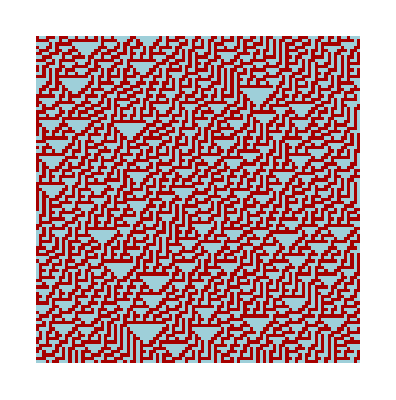

```mathematica
ArrayPlot[CellularAutomaton[30,RandomInteger[1,100],100]]
```

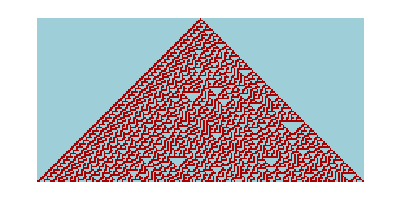

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},100]]
```

```mathematica
ArrayPlot[CellularAutomaton[146,RandomInteger[1,500],500]]
```

-Graphics-

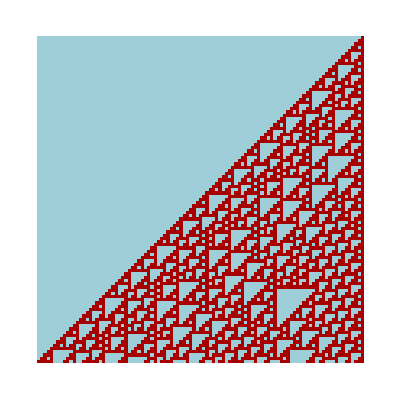

```mathematica
ArrayPlot[CellularAutomaton[110, {{1}, 0}, 100]]
```

```mathematica
ArrayPlot[car=CellularAutomaton[30, {{1},0}, 500]]
```

-Graphics-

```mathematica
Length[car⟦1⟧]
```

```mathematica
1001
randomList=car[[All,501]]
```

1001

{1,1,0,1,1,1,0,0,1,1,0,0,0,1,0,1,1,0,0,1,0,0,1,1,1,0,1,0,1,1,1,0,0,1,1,1,0,1,0,1,0,1,1,0,0,0,0,1,1,0,0,1,0,1,0,1,1,0,1,0,1,0,1,1,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,1,0,1,0,1,1,1,0,0,0,0,0,1,0,0,1,0,1,1,0,0,0,1,1,1,0,0,0,1,1,0,1,1,0,1,1,0,1,0,0,0,0,0,0,0,1,0,0,0,1,1,1,1,1,0,1,1,1,0,1,0,0,1,1,1,0,0,0,1,1,1,0,1,0,1,1,1,0,0,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,1,1,1,1,0,0,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,1,1,1,0,1,1,0,0,1,0,1,1,0,1,1,1,0,0,0,0,0,1,0,1,1,0,0,0,1,1,0,1,1,0,0,0,1,1,0,0,0,1,1,1,0,1,1,0,1,1,0,0,1,0,1,0,1,1,1,1,1,1,1,0,1,1,0,1,0,1,1,0,1,1,0,1,1,1,1,0,1,1,1,0,0,1,0,1,1,1,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,0,0,1,0,1,1,0,0,1,0,1,1,1,1,0,0,1,0,0,1,1,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,1,0,1,1,0,1,1,0,0,1,1,1,1,0,0,1,0,0,0,0,1,0,0,1,1,1,1,1,0,0,0,0,0,1,1,0,1,0,0,1,0,1,1,0,0,1,0,0,1,0,1,1,1,0,1,0,1,1,0,0,0,0,0,1,1,0,1,0,0,1,0,0,0,1,0,1,0,0,1,0,1,1,1,0,1,0,1,1,1,1,1,0,1,1,0,0,0,1,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,0,0,1,1,1,1,0,1,0,0,1,0,1,1,0,1,0,0,0,1,1,0,1,0,0,0,1,1,1,1,0,0,0,0,1,0,0,0,0,1,1,1,1,0}

```mathematica
randomDigits=FromDigits[#,2]&/@Partition[randomList, 4]
```

{13,12,12,5,9,3,10,14,7,5,6,1,9,5,10,11,15,0,15,1,5,12,1,2,12,7,1,11,6,8,0,8,15,11,10,7,1,13,7,0,6,4,6,7,9,15,8,1,15,13,9,6,14,0,11,1,11,1,8,14,13,9,5,15,13,10,13,11,13,12,11,11,1,0,0,3,7,2,12,11,12,9,8,7,12,0,11,6,7,9,0,9,15,0,6,9,6,4,11,10,12,1,10,4,5,2,14,11,14,12,4,0,15,5,1,14,9,6,8,13,1,14,1,0,15}

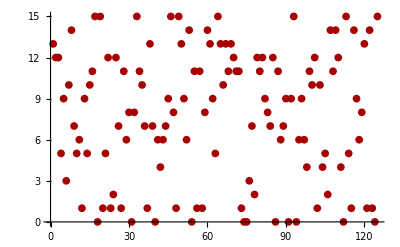

```mathematica
ListPlot[randomDigits]
```

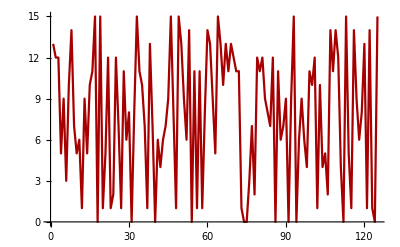

```mathematica
ListLinePlot[randomDigits]
```

```mathematica
Counts[randomDigits]
```

<|13→8,12→10,5→7,9→10,3→2,10→6,14→7,7→8,6→9,1→13,11→12,15→9,0→11,2→3,8→6,4→4|>

```mathematica
Counts[RealDigits[N[Pi,1000]]⟦1⟧]
```

<|3→103,1→116,4→93,5→97,9→106,2→103,6→94,8→100,7→95,0→93|>

```mathematica
N[StandardDeviation[RealDigits[N[Pi, 1000]][[1]]]]
N[StandardDeviation[FromDigits[#,2]&/@Partition[
CellularAutomaton[30, {{1}, 0}, 1000]⟦1001,All⟧, 4]]]
N[StandardDeviation[RandomInteger[15,1000]]]
```

2.90027

4.61004

4.68891

## Classificação do ECA: IV Classes

```mathematica
Manipulate[
ArrayPlot[
CellularAutomaton[rule,RandomInteger[1,100],100],
PlotLabel-> rule],
{rule,0,255,1}]
```

```mathematica
Manipulate[ArrayPlot[
CellularAutomaton[rule, {{1},0}, {size,All}], 
PlotLabel -> rule,Mesh->mesh],
 {rule, 0, 255, 1},
{size,10,100,1},
{mesh,{False,True}}]
```

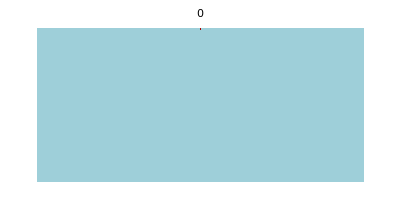
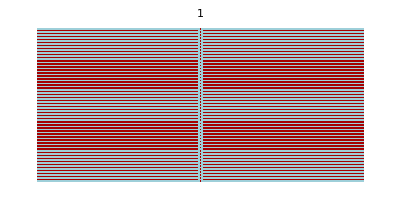
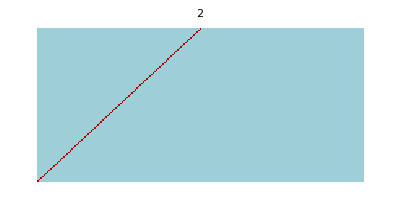
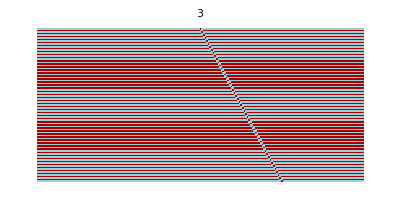
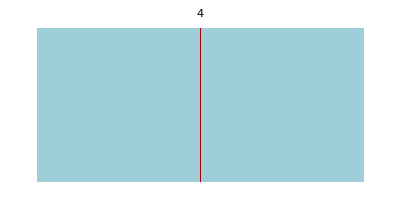
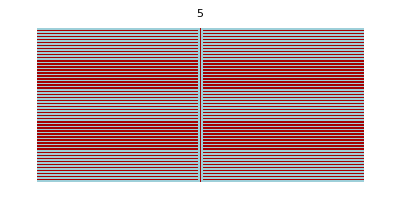
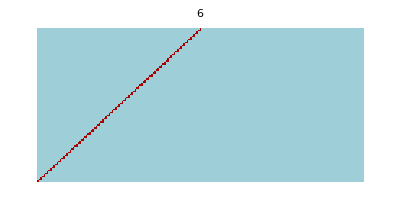
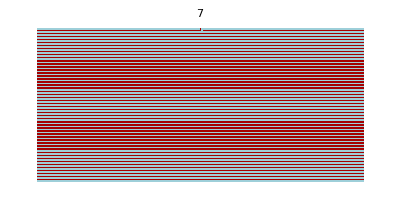
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[
CellularAutomaton[rule, {{1}, 0}, {100, All}],
 PlotLabel -> rule],
{rule,0,255,1}]
```

Classe I : Converge para uma única cor
Classe II : Padrão repetitivo
Classse III : Aleatório
Classe IV : Padrões repetitivos e aleatórios (Classe II + III)

```mathematica
Manipulate[
RandomSeed[seed];
Grid[
{{ArrayPlot[ca=CellularAutomaton[rule, RandomInteger[1, 100], 100], 
PlotLabel -> rule,Frame-> None],
ListLinePlot[Total[Transpose[ca]]]}}],
 {rule, 0, 255, 1},
{seed,1,1000,1}]
```

## + cores (k) e vizinhos (r)

CA com 3 Cores k==3
e vizinhança de 3 células r==1 
regra número 921408

```mathematica
ArrayPlot[CellularAutomaton[{888921408,3,1},{{1},0},100],
ColorRules-> {0-> White,1-> Yellow,2-> Orange}]
```

-Graphics-

Enumeração

```mathematica
k^k^(2*r+1)
3^3^((2*1)+1)
```

k^(k^(1+2 r))

7625597484987

Cor k==3
Vizinhança r==1 
Regra totalistica 867

```mathematica
ArrayPlot[cat=CellularAutomaton[{867, {3, 1}, 1}, {{1}, 0}, 100],ColorFunction->"Rainbow",Frame-> None]
```

-Graphics-

One to Zero Cellular Automaton Function

```mathematica
UpToOne[n_List]:= If[#>1,0,#]&[Apply[Plus,n]];

Manipulate[
SeedRandom[seed];
ArrayPlot[CellularAutomaton[{UpToOne[#]&,{},1},RandomReal[1,size],size],ColorFunction-> color,Frame-> None, ImageSize-> {350,350}],
{{size,150},10,400,1},
{{seed,100,"random seed"},1,10000000,1},
{{color,"DarkRainbow"},#-> Show[ColorData[#,"Image"], ImageSize-> 120] &/@ ColorData["Gradients"]},SaveDefinitions->True
]
```

-Graphics-

## CA 2D

-Graphics-

CA 2D 5 vizinhos  totalistico

```mathematica
ArrayPlot[CellularAutomaton[{26, {2, {
{0, 1, 0}, 
{1, 1, 1}, 
{0, 1, 0}}}, 
{1, 1}}, {{{1}}, 0}, {{{100}}}]]
```

-Graphics-

CA 2D 9 vizinhos totalistico

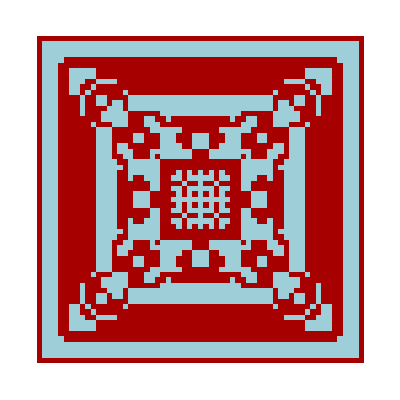

```mathematica
ArrayPlot[CellularAutomaton[{14, {2, 1}, {1, 1}}, {{{1}}, 0}, {{{30}}}]]
```

Acumulando a média das etapas...

```mathematica
Manipulate[ArrayPlot[Mean[CellularAutomaton[{14, {2, 1}, {1, 1}}, {{{1}}, 0}, step]],ColorFunction-> Hue],{step,1,100,1}]
```

Exibe cubo no lugar de cada célula preta (1):

```mathematica
Manipulate[Graphics3D[Cuboid /@ Position[
CellularAutomaton[{14, {2, 1}, {1, 1}}, {{{1}}, 0}, step], 1], 
ViewVertical -> {-1, 0, 0}],{step,1,30,1}]
```

#### Cluster CA

```mathematica
Manipulate[
SeedRandom[rseed];
ArrayPlot[ca=CellularAutomaton[{52,{2,{{0,1,0},{1,1,1},{0,1,0}}},{1,1}},RandomInteger[1,{size,size}],{{{steps}}}],Frame-> None,ImageSize-> {350,350},PlotLabel-> Text[Row[{"white cells == ",Count[Flatten[ca],0],Style["  |  ",Blue],"black cells == ",Count[Flatten[ca],1]}]],ColorRules-> If[color,{0-> Yellow,1-> Orange},{0-> White,1-> Black}]],
{{steps,500},0,500,1,Appearance->"Labeled"},
{{size,100},10,100,Appearance->"Labeled"},
{{rseed,1,"random seed"},0,100000,1},
{color,{False,True}},SaveDefinitions->True,TrackedSymbols->True]
```

3D Layers Evolution of Five-Neighbor Outer Totalistic 2D Cellular Automaton

```mathematica
Manipulate[
 Module[{objects}, objects = Cuboid[#] & /@ Position[
CellularAutomaton[{rule, {2, {{0, 2, 0}, {2, 1, 2}, {0, 2, 0}}}, {1, 1}}, {{{1}}, 0}, {step}], plot];
  Graphics3D[Prepend[Prepend[Riffle[Table[
ColorData[color, c], {c, 0, 1, If[objects === {}, 1, 1/Length[objects]]}], objects], 
Opacity[opacity]], EdgeForm[Darker[Gray]]], Boxed -> False, ViewVertical -> {-1, 0, 0}, 
ImageSize -> {400, 400}, Background -> Black]],
 {{rule, 355}, 0, 1023, 1, Appearance -> "Labeled"},
 {{step, 5, "steps"}, 0, 8, 1, Appearance -> "Labeled"},
 {{opacity, 1}, 0, 1},
 {{color, "SouthwestColors"}, Flatten[Rule[#, 
Show[ColorData[#, "Image"], ImageSize -> 80]] & /@ ColorData["Gradients"]]},
 {{plot, 1}, {1 -> "1 cells", 0 -> "0 cells"}},
 AutorunSequencing -> {1, 2},
 TrackedSymbols -> True]
```

## Game of Life

Conway’s Game of Life
 
2D CA Totalistico:  game of life

Regras Simples:

Qualquer célula viva com menos de dois vizinhos vivos morre de solidão.

Qualquer célula viva com mais de três vizinhos vivos morre de superpopulação.

Qualquer célula morta com exatamente três vizinhos vivos se torna uma célula viva.

Qualquer célula viva com dois ou três vizinhos vivos continua no mesmo estado para a próxima geração.

Célula viva = 1, preto
Célular morta = 0, branco

Vizinhança de Moore:
-Graphics-

Logo Hacker: Glider

-Graphics-

Glider!!

```mathematica
arrayPlot[initialCondition_, mesh_, color_] := 
ArrayPlot[initialCondition, Mesh -> mesh, 
ColorRules -> If[color, {1 -> Orange, 0 -> Yellow}, 
{1 -> Black, 0 -> White}], ImageSize -> 350, Frame -> False];

hackerPlot[initialCondition_, mesh_, color_] := 
GraphicsGrid[
Map[If[# == 1, Graphics[{If[color, Orange, Black], Disk[]}], ""] &, 
initialCondition, {2}], Frame -> mesh, FrameStyle -> Gray, 
Spacings -> 2, Background -> If[color, Yellow, White] ];

Manipulate[
Pane[view[CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},
SparseArray[If[matrixSize>3,
Append[#,{matrixSize,matrixSize}-> 0],#]&
[{{1,2}-> 1,{2,3}-> 1,{3,1}-> 1,{3,2}-> 1,{3,3}-> 1}]],
{{{step}}}],mesh,color],{350,350}],
{{matrixSize,10,"matrix size"},3,15,1},
{step,0,100,1},
{{view,hackerPlot},{hackerPlot-> "hacker",arrayPlot-> "traditional"}},
{{mesh,All},{All-> "yes",None-> "no"}},
{color,{False,True},ControlType-> Checkbox},SaveDefinitions->True,
AutorunSequencing->{1,2,3,5}]
```

Turbina (Pattern)

```mathematica
initialCondition = {
   {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},
   {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},
   {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},
   {0, 0, 0, 1, 1, 1, 1, 1, 1, 0, 1, 1, 0, 0, 0},
   {0, 0, 0, 1, 1, 1, 1, 1, 1, 0, 1, 1, 0, 0, 0},
   {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0},
   {0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0},
   {0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0},
   {0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0},
   {0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},
   {0, 0, 0, 1, 1, 0, 1, 1, 1, 1, 1, 1, 0, 0, 0},
   {0, 0, 0, 1, 1, 0, 1, 1, 1, 1, 1, 1, 0, 0, 0},
   {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},
   {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},
   {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
   }; (* turbine *)
```

```mathematica
Manipulate[
 ArrayPlot[CellularAutomaton[{224, 
{2, {
{2, 2, 2}, 
{2, 1, 2}, 
{2, 2, 2}}}, {1, 1}}, initialCondition, 
{{{step}}}], Mesh -> mesh, ColorRules -> If[color, 
{1 -> Orange, 0 -> Yellow}, {1 -> Black, 0 -> White}], ImageSize -> 400],
 {step, 0, 16, 1, Appearance -> "Labeled"},
 {mesh, {None, All}, ControlType -> Checkbox},
 {color, {True, False}, ControlType -> Checkbox}, SaveDefinitions -> True]
```

```mathematica
rand=RandomInteger[1,{200,200}];
Manipulate[

  ArrayPlot[CellularAutomaton[{224, 
    {2, {
      {2, 2, 2}, 
      {2, 1, 2}, 
      {2, 2, 2}}}, {1, 1}}, rand, 
   {{{step}}}], Mesh -> mesh, ColorRules ->
 If[color, 
    {1 -> Orange, 0 -> Yellow},
 {1 -> Black, 0 -> White}], ImageSize -> 400],
  {step, 0, 200, 1, Appearance -> "Labeled"},
  {mesh, {None, All}, ControlType -> Checkbox},
  {color, {True, False}, ControlType -> Checkbox}, 
SaveDefinitions -> True]
```

```mathematica
gameOfLife = {224, {2, {{2, 2, 2}, {2, 1, 2}, {2, 2, 2}}}, {1, 1}};
rand2=RandomInteger[1, {200, 200}];
ArrayPlot[Mean[CellularAutomaton[gameOfLife, rand2, 400]],
ColorFunction-> Hue]
```

-Graphics-

```mathematica
Manipulate[ArrayPlot[Mean[CellularAutomaton[gameOfLife, rand2, step]], 
ColorFunction -> Hue],{step,1,200,1}]
```

Video: https://www.youtube.com/watch?v=C2vgICfQawE
Demonstrations: http://demonstrations.wolfram.com/

## Referências:

-Graphics-

http://www.wolframscience.com/

http://www.wolframscience.com/nksonline/toc.html

http://mathworld.wolfram.com/CellularAutomaton.html

https://www.openabm.org/book/export/html/1949

Cellular Automata and the Mechanisms of Nature

http://mathworld.wolfram.com/TotalisticCellularAutomaton.html

http://pt.wikipedia.org/wiki/Jogo_da_vida

https://www.garoa.net.br/wiki/Celebration_of_Mind

http://celebrationofmind.org/

http://en.wikipedia.org/wiki/Martin_Gardner